```mathematica
■Analisis MAV
```

MAV ■Analisis

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{NotebookDirectory[],"Extra","AdvancedMapping.wl"}]];
Needs["EconomicComputations`",FileNameJoin[{NotebookDirectory[],"EconomicComputations.wl"}]];

(* Opciones de estilo *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,ColorData["Legacy"]["Olive"]};
```

## Cargar base de datos

```mathematica
path = FileNameJoin[{NotebookDirectory[],"DJI_DAX_MXX_NIKKEI_dataset.mx"}];
database = Import[path];
database[[All,"Name"]] = {"DJIA","DAX","IPC","Nikkei 225"};
```

## Fechas percentuales

```mathematica
DaysInYear[year_] := First[DateDifference[{year, 1, 1}, {year, 12, 31}]] + 1;

YearPercentual[date_] := N[QuantityMagnitude[DateDifference[DateObject[{date["Year"], 1, 1}], date]] / DaysInYear[date["Year"]]] + date["Year"];

DateFromYearPercentual[yearPercentual_] := Block[{year, daysEllapsed, date},
	year = IntegerPart[yearPercentual];
	daysEllapsed = IntegerPart[(yearPercentual - year) * DaysInYear[year]];
	date = DatePlus[DateObject[{year, 1, 1}], daysEllapsed];
	Return[date];
];
```

```mathematica
Ventana[market_,dias_]:=MovingAverage[MapAt[YearPercentual, database[[market]]["DatedPrices"], {All,1}],dias];
```

rVentana arroja las fechas percentuales con los precios

```mathematica
rVentana = Ventana[1, 50];
```

DateFromYearPercentual cambia el formato de fecha de percentual a formato de fecha de mathematica

MAVDates devuelve las fechas en formato de fecha de mathematica

```mathematica
MAVDates = Map[DateFromYearPercentual[#] &, rVentana[[All, 1]]];
```

Se asignan a cada una de las fechas los precios. Fecha y precio será arrojada por MAVResult

```mathematica
MAVPrices = rVentana[[All, 2]];
MAVResult = Transpose[{MAVDates, MAVPrices}]
```

{{Day: Mon 16 Dec 1991,1597.36},{Day: Wed 18 Dec 1991,1598.91},{Day: Thu 19 Dec 1991,1600.39},6411,{Day: Wed 26 Apr 2017,12405.6},{Day: Thu 27 Apr 2017,12422.9},{Day: Sat 29 Apr 2017,12438.6}}
 |  |  |  |

Pero MAVResult es lo mismo que MAVDatePrice

```mathematica
MAVDatePrice = Transpose[{MAVDates, MAVPrices}];
ReturnLogs = MAVDatePrice[[All, 2]] // Returns;
DatesLogReturn = Drop[MAVDatePrice[[All, 1]], -1];
MAVReturn = Transpose[{DatesLogReturn, ReturnLogs}];
```

```mathematica
cuartiles = Quantile[MAVReturn[[All, 2]], {1/4, 1/2, 3/4}]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Quantile[Symbol[],{1/4,1/2,3/4}]

```mathematica
MAVReturn
```

{{Day: Mon 16 Dec 1991,0.000968629},{Day: Wed 18 Dec 1991,0.000926452},{Day: Thu 19 Dec 1991,0.00063964},6410,{Day: Mon 24 Apr 2017,0.000987167},{Day: Wed 26 Apr 2017,0.00138681},{Day: Thu 27 Apr 2017,0.00126461}}
 |  |  |  |

Calcular sigma, mu , aquí, del resultado de los retornos de MAV

De los retornos de los datos reales, se obtiene μ y σ , y son utilizados para simular retornos por medio de un caminante aleatorio.

```mathematica
MeanReturns=Mean[MAVReturn[[All,2]]];
stdReturns=StandardDeviation[MAVReturn[[All,2]]];
randomV= RandomVariate[NormalDistribution[MeanReturns,stdReturns],Length[MAVReturn[[All,2]]]];

(*BuscarPrecio[datedPrices_,date_]:=FirstCase[datedPrices,{date,p_}:>p];
(*La siguiente linea de codigo nos da todas las fechas en que se tuvo minima entropia y su precio*)
Rastreador = Map[{#,BuscarPrecio[database[[market]]["DatedPrices"],#]}&,MercadoNoGaussiano[[All,1]]]*)
```

En esta parte se estandarizan los retornos, tanto reales, como lo simulados.

```mathematica
returnRealEstandarizado=Standardize[MAVReturn[[All,2]]];
```

```mathematica
returnSimuladosEstandarizados=Standardize[randomV];
```

```mathematica
Qreal=Quantile[returnRealEstandarizado,{1/4,1/2,3/4}];
Qsimula=Quantile[returnSimuladosEstandarizados,{1/4,1/2,3/4}];
```

```mathematica
intervaloReales=Partition[Join[{-∞},Qreal,{∞}],2,1];
intervaloSimulados=Partition[Join[{-∞},Qsimula,{∞}],2,1];
reglas[intervalo_]:=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalo,Range[4]}];
intervaloRDiscretizado=reglas[intervaloReales];
intervaloSDiscre=reglas[intervaloSimulados];
```

En la siguiente linea se obtienen los retornos discretizados

```mathematica
returnsDiscretosReales=returnRealEstandarizado/.intervaloRDiscretizado;
```

```mathematica
returnDiscretSimulados=returnSimuladosEstandarizados/.intervaloSDiscre;
```

Se acomoda fecha y valor de retorno discretizado, tanto para el real como para el simulado.

```mathematica
fechaReal=Drop[database[[1]]["Dates"],-50];
```

A continuacion viene fecha y dato para los valores del mercado real

```mathematica
FechaRetornoReal=Transpose[{fechaReal,returnsDiscretosReales}];
```

Lo mismo se hace para los datos simulados

```mathematica
FechaRetornoSimulado=Transpose[{fechaReal,returnDiscretSimulados}];
```

### Calculando entropías

Se ocupa una partición para cada uno, una particion para los retornos reales  y una partición para los simulados

```mathematica
particionRetReal[dias_]:=Partition[FechaRetornoReal,dias,1];
particionRetornoSimulados[dias_]:=Partition[FechaRetornoSimulado,dias,1];
```

### Entropia de los retornos reales

```mathematica
Sreal=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetReal[50]];
```

```mathematica
Entropia de los retornos simulados
```

```mathematica
SSimulada=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,particionRetornoSimulados[50]];
```

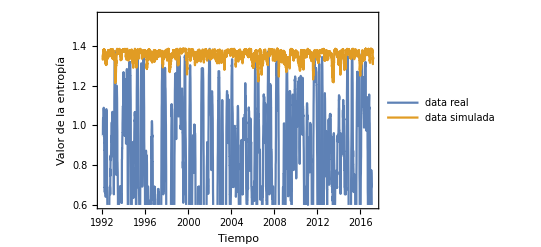

```mathematica
DateListPlot[{Sreal,SSimulada},PlotRange->{0.6,1.55},Frame->True,FrameLabel->{{"Valor de la entropía","2017"},{"Tiempo","Entropía de retornos reales y simulados"}},PlotLegends->{"data real", "data simulada"}]
```

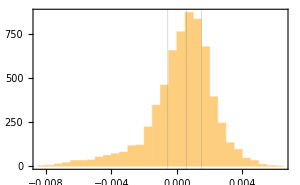

```mathematica
a=Histogram[MAVReturn[[All,2]],GridLines->{cuartiles,{}},PlotRange-> All,Frame-> True]
```

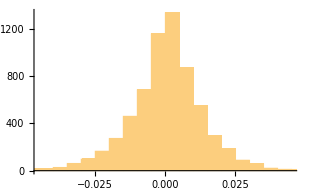

```mathematica
b=Histogram[database[[1]]["Returns"]]
```

```mathematica
intervalos=Partition[Join[{-∞},cuartiles,{∞}],2,1]
```

{{-∞,-0.000556771},{-0.000556771,0.000587268},{0.000587268,0.00151629},{0.00151629,∞}}

```mathematica
discreteStates=Range[Length[intervalos]];
reglas=MapThread[(x_/;IntervalMemberQ[Interval[#1],x])->#2&,{intervalos,discreteStates}];

resultado=MAVReturn[[All,2]]/.reglas;
```

```mathematica
discretoConFechas=Transpose[{MAVReturn[[All,1]],resultado}]
```

```mathematica
Length[discretoConFechas]
```

6416

```mathematica
window=50;
```

```mathematica
parts=Partition[discretoConFechas,window,1];
resultado=Map[{Last[#[[All,1]]],N[Entropy[#[[All,2]]]]}&,parts];
```

```mathematica
i=1
```

1

```mathematica
Last[resultado]
```

{Day: Thu 27 Apr 2017,0.265158}

```mathematica
parts[[i]][[All,2]]
```

```mathematica
For[i=1,i<6367,i++,Print[N[Entropy[parts[[i]][[All,2]]]]]];
```

```mathematica
N[Entropy[parts[[i]][[All,2]]]]
```

0.948693

```mathematica
(*For[i=1,i<6367,i++,Print[N[Entropy[parts[[i]][[All,2]]]]]];*)
```

```mathematica
parts[[6367]]
```

{{Day: Wed 15 Feb 2017,3},{Day: Fri 17 Feb 2017,3},{Day: Sat 18 Feb 2017,3},{Day: Sun 19 Feb 2017,3},{Day: Tue 21 Feb 2017,3},{Day: Wed 22 Feb 2017,3},{Day: Fri 24 Feb 2017,3},{Day: Sat 25 Feb 2017,3},{Day: Sun 26 Feb 2017,3},{Day: Tue 28 Feb 2017,3},{Day: Wed 1 Mar 2017,3},{Day: Fri 3 Mar 2017,3},{Day: Sat 4 Mar 2017,3},{Day: Sun 5 Mar 2017,3},{Day: Tue 7 Mar 2017,3},{Day: Wed 8 Mar 2017,3},{Day: Fri 10 Mar 2017,2},{Day: Sat 11 Mar 2017,3},{Day: Mon 13 Mar 2017,3},{Day: Tue 14 Mar 2017,3},{Day: Wed 15 Mar 2017,3},{Day: Fri 17 Mar 2017,3},{Day: Sat 18 Mar 2017,3},{Day: Mon 20 Mar 2017,3},{Day: Tue 21 Mar 2017,3},{Day: Thu 23 Mar 2017,3},{Day: Fri 24 Mar 2017,3},{Day: Sun 26 Mar 2017,3},{Day: Mon 27 Mar 2017,3},{Day: Wed 29 Mar 2017,3},{Day: Thu 30 Mar 2017,3},{Day: Sat 1 Apr 2017,4},{Day: Sun 2 Apr 2017,3},{Day: Tue 4 Apr 2017,4},{Day: Wed 5 Apr 2017,3},{Day: Fri 7 Apr 2017,3},{Day: Sat 8 Apr 2017,3},{Day: Mon 10 Apr 2017,3},{Day: Tue 11 Apr 2017,3},{Day: Wed 12 Apr 2017,3},{Day: Fri 14 Apr 2017,3},{Day: Sat 15 Apr 2017,3},{Day: Mon 17 Apr 2017,3},{Day: Tue 18 Apr 2017,3},{Day: Thu 20 Apr 2017,3},{Day: Fri 21 Apr 2017,3},{Day: Sun 23 Apr 2017,3},{Day: Mon 24 Apr 2017,3},{Day: Wed 26 Apr 2017,3},{Day: Thu 27 Apr 2017,3}}

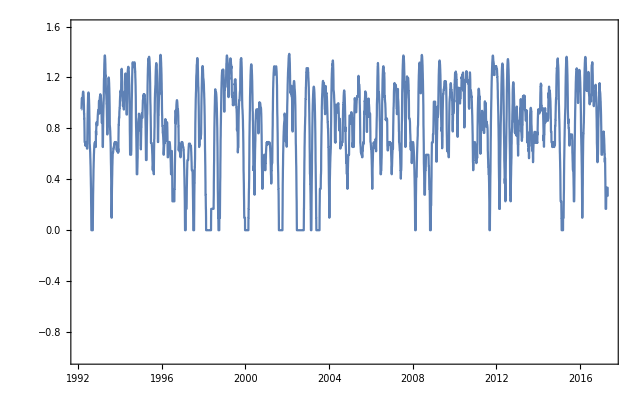

```mathematica
DateListPlot[resultado, PlotRange->{-1,1.6}]
```

```mathematica
Last[parts[[All,1]]]
```

{Day: Wed 15 Feb 2017,3}

```mathematica
Last[parts[[All,2]]]
```

{Day: Fri 17 Feb 2017,3}

```mathematica
parts
```

{{{Day: Mon 16 Dec 1991,3},{Day: Wed 18 Dec 1991,3},{Day: Thu 19 Dec 1991,3},{Day: Sat 21 Dec 1991,3},{Day: Mon 23 Dec 1991,3},{Day: Tue 24 Dec 1991,3},{Day: Thu 26 Dec 1991,3},{Day: Fri 27 Dec 1991,3},{Day: Sun 29 Dec 1991,3},{Day: Mon 30 Dec 1991,3},{Day: Wed 1 Jan 1992,3},{Day: Thu 2 Jan 1992,3},{Day: Sat 4 Jan 1992,3},{Day: Mon 6 Jan 1992,3},{Day: Tue 7 Jan 1992,3},{Day: Thu 9 Jan 1992,4},{Day: Fri 10 Jan 1992,4},{Day: Sun 12 Jan 1992,4},{Day: Mon 13 Jan 1992,4},{Day: Wed 15 Jan 1992,4},{Day: Thu 16 Jan 1992,4},{Day: Sat 18 Jan 1992,4},{Day: Sun 19 Jan 1992,4},{Day: Tue 21 Jan 1992,4},{Day: Wed 22 Jan 1992,4},{Day: Fri 24 Jan 1992,4},{Day: Sun 26 Jan 1992,4},{Day: Mon 27 Jan 1992,4},{Day: Wed 29 Jan 1992,4},{Day: Thu 30 Jan 1992,4},{Day: Sat 1 Feb 1992,4},{Day: Sun 2 Feb 1992,4},{Day: Tue 4 Feb 1992,4},{Day: Wed 5 Feb 1992,3},{Day: Fri 7 Feb 1992,4},{Day: Sat 8 Feb 1992,3},{Day: Sun 9 Feb 1992,4},{Day: Tue 11 Feb 1992,4},{Day: Wed 12 Feb 1992,4},{Day: Fri 14 Feb 1992,3},{Day: Sat 15 Feb 1992,3},{Day: Sun 16 Feb 1992,3},{Day: Tue 18 Feb 1992,2},{Day: Wed 19 Feb 1992,3},{Day: Fri 21 Feb 1992,2},{Day: Sat 22 Feb 1992,2},{Day: Sun 23 Feb 1992,2},{Day: Tue 25 Feb 1992,2},{Day: Wed 26 Feb 1992,3},{Day: Fri 28 Feb 1992,3}},{1},6364,{{Day: Wed 15 Feb 2017,3},{Day: Fri 17 Feb 2017,3},{Day: Sat 18 Feb 2017,3},{Day: Sun 19 Feb 2017,3},{Day: Tue 21 Feb 2017,3},{Day: Wed 22 Feb 2017,3},{Day: Fri 24 Feb 2017,3},{Day: Sat 25 Feb 2017,3},{Day: Sun 26 Feb 2017,3},{Day: Tue 28 Feb 2017,3},{Day: Wed 1 Mar 2017,3},{Day: Fri 3 Mar 2017,3},{Day: Sat 4 Mar 2017,3},{Day: Sun 5 Mar 2017,3},{Day: Tue 7 Mar 2017,3},{Day: Wed 8 Mar 2017,3},{Day: Fri 10 Mar 2017,2},{Day: Sat 11 Mar 2017,3},{Day: Mon 13 Mar 2017,3},{Day: Tue 14 Mar 2017,3},{Day: Wed 15 Mar 2017,3},{Day: Fri 17 Mar 2017,3},{Day: Sat 18 Mar 2017,3},5,{Day: Mon 27 Mar 2017,3},{Day: Wed 29 Mar 2017,3},{Day: Thu 30 Mar 2017,3},{Day: Sat 1 Apr 2017,4},{Day: Sun 2 Apr 2017,3},{Day: Tue 4 Apr 2017,4},{Day: Wed 5 Apr 2017,3},{Day: Fri 7 Apr 2017,3},{Day: Sat 8 Apr 2017,3},{Day: Mon 10 Apr 2017,3},{Day: Tue 11 Apr 2017,3},{Day: Wed 12 Apr 2017,3},{Day: Fri 14 Apr 2017,3},{Day: Sat 15 Apr 2017,3},{Day: Mon 17 Apr 2017,3},{Day: Tue 18 Apr 2017,3},{Day: Thu 20 Apr 2017,3},{Day: Fri 21 Apr 2017,3},{Day: Sun 23 Apr 2017,3},{Day: Mon 24 Apr 2017,3},{Day: Wed 26 Apr 2017,3},{Day: Thu 27 Apr 2017,3}}}
 |  |  |  |

```mathematica
fechas=Drop[database[[1]]["Dates"],-1];
returns1=database[[1]]["Returns"];
```

```mathematica
MovingAverage[returns1,50]
```

```mathematica
Drop[fechas,-1]
```

6464